3.1 Lorenz model
a)

```mathematica
x=.;y=.;z=.;S=.;stabMat =.; f=.;g=.;h=.;sigma=.;r=.;b=.;
Remove[flow]

f = sigma*(y-x);
g = r*x-y-x*z;
h = x*y-b*z;
sigma=10;
b=8/3;
r=28;
flow = {f,g,h};

S = NSolve[flow==0,{x,y,z}];
stabMat = D[flow,{{x,y,z}}]/.%[[2]]; 
Eigenvalues[stabMat]

lim=20;
StreamPlot3D[flow,{x,-lim,lim},{y,-lim,lim},{z,-lim,lim}];
```

{-13.8546+0. ⅈ,0.0939556+10.1945 ⅈ,0.0939556-10.1945 ⅈ}

b)

```mathematica
x=.;y=.;z=.;S=.;stabMat =.;T=.;t=.;Tmax=.;p0=.;sol=.;t=.;T=.;
system = {x'[t]==sigma*(y[t]-x[t]),y'[t]==r*x[t]-y[t]-x[t]*z[t], z'[t]==x[t]*y[t]-b*z[t]};
sol[T_]:=NDSolve[Join[system,Thread[{x[0],y[0], z[0]}==5]],{x[t],y[t], z[t]},{t,0,T}];
Tmax = 20;
p0 = Show[ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol[Tmax]],{t,0,Tmax},PlotStyle->Green,PlotRange->{{-40,40},{-40,40}, {-0,50}}, AxesLabel -> {x,y,z}]];
(p0//Normal)/.Line[x_]:>{Arrowheads[{0.05,0.05,0.05,0.05, 0.05}],Arrow[x], PlotStyle-> Black}
```

-Graphics3D-

3. 2
a)

```mathematica
rdot=.;thetadot=.;μ=.; ω=.;ν=.;r=.;S=.;

rdot = μ*r-r^3;
S =r/.NSolve[rdot==0,{r}];
r0 = S[[3]];
r = r0;

thetadot = ω + ν*r^2;
Tperiod = 2 Pi / thetadot;

{r0,Tperiod}
```

{√μ,(2 π)/(μ ν+ω)}

b)

```mathematica
X1=.;X2=.;DynSys=.;X1Dot=.;X2Dot=.;sol=.;flow=.;

X1Dot = .1 X1[t]-X2[t]^3-X1[t] X2[t]^2-X1[t]^2 X2[t] -X2[t] -X1[t]^3;
X2Dot = X1[t] +.1 X2[t]+X1[t]X2[t]^2 + X1[t]^3-X2[t]^3-X1[t]^2  X2[t] ;
DynSys = {X1'[t]==X1Dot,X2'[t]==X2Dot};
flow = {.1 X1-X2^3-X1 X2^2-X1^2 X2 -X2 -X1^3,X1 +.1 X2+X1 X2^2 + X1^3-X2^3-X1^2  X2};


sol[T_]:= NDSolve[Join[DynSys,Thread[{X1[0],X2[0]}== {Sqrt[.1], 0}]],{X1[t],X2[t]},{t,0,T}];

lim= 1;
Tmax = 200;
p0 =Show[StreamPlot[flow,{X1,-lim,lim},{X2,-lim,lim}],ParametricPlot[Evaluate[{X1[t],X2[t]}/.sol[Tmax]],{t,0,Tmax},PlotStyle->Green,PlotRange->{{-lim,lim},{-lim,lim}}]];
```

c)

```mathematica
theta=.; r=.;X1=.;X2=.;flow=.;
X1 = r Cos[theta];
X2 = r Sin[theta];
flow = {.1 X1-X2^3-X1 X2^2-X1^2 X2 -X2 -X1^3,X1 +.1 X2+X1 X2^2 + X1^3-X2^3-X1^2  X2};
Simplify[flow]//MatrixForm
μ = .1;
ν = 1;
ω = 1;
```

((0.1 r-1. r^3) Cos[theta]+r (-1.-1. r^2) Sin[theta]
(1. r+1. r^3) Cos[theta]+r (0.1-1. r^2) Sin[theta])

d)

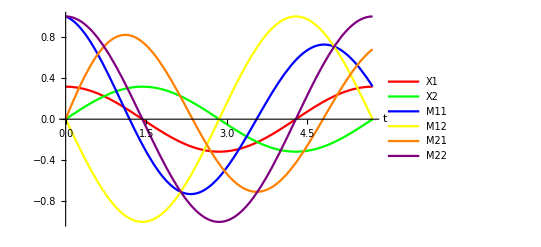

```mathematica
X1=.;X2=.;X1Dot=.;X2Dot=.;DynSys=.;ClearAll[X1];ClearAll[X2];ClearAll[M11];ClearAll[M12];ClearAll[M21];ClearAll[M22]

X1Dot = .1 X1[t]-X2[t]^3-X1[t] X2[t]^2-X1[t]^2 X2[t] -X2[t] -X1[t]^3;
X2Dot = X1[t] +.1 X2[t]+X1[t]X2[t]^2 + X1[t]^3-X2[t]^3-X1[t]^2  X2[t] ;
stabMat = D[{X1Dot,X2Dot}, {{X1[t],X2[t]}}];

DynSys = {X1'[t]==X1Dot,X2'[t]==X2Dot};
sol = NDSolve[Join[{DynSys, M11'[t] == stabMat[[1]][[1]]*M11[t]+stabMat[[1]][[2]]*M21[t], M12'[t] == stabMat[[1]][[1]]*M12[t]+stabMat[[1]][[2]]*M22[t], M21'[t] == stabMat[[2]][[1]]*M11[t]+stabMat[[2]][[2]]*M21[t], M22'[t]==stabMat[[2]][[1]]*M12[t]+stabMat[[2]][[2]]*M22[t],X1[0] == 1/Sqrt[10], X2[0]== 0, M11[0] == 1, M12[0]== 0, M21[0]==0,M22[0]==1}],{X1[t],X2[t], M11[t],M12[t],M21[t],M22[t]},{t,0,Tmax}];


p1 = Plot[{X1[t]}/.sol, {t, 0, Tperiod}, PlotStyle-> Red, PlotLegends-> {"X1"}, AxesLabel->{"t", ""}];
p2 = Plot[X2[t]/.sol, {t, 0, Tperiod}, PlotStyle->Green, PlotLegends-> {"X2"}];
p3 = Plot[M11[t]/.sol, {t, 0, Tperiod}, PlotStyle-> Blue, PlotLegends-> {"M11"}];
p4 = Plot[M12[t]/.sol, {t, 0, Tperiod}, PlotStyle-> Yellow, PlotLegends-> {"M12"}];
p5 = Plot[M21[t]/.sol, {t, 0, Tperiod}, PlotStyle-> Orange, PlotLegends-> {"M21"}];
p6 = Plot[M22[t]/.sol, {t, 0, Tperiod}, PlotStyle->Purple, PlotLegends-> {"M22"}];
plot = Show[p1, p2, p3, p4, p5, p6, PlotRange-> Automatic]
```

e)

```mathematica
t=Tperiod;
M11 = M11[t]/.sol
M12 = M12[t]/.sol
M21 = M21[t]/.sol
M22 = M22[t]/.sol
```

{0.319053}

{1.659×10^-8}

{0.680946}

{0.999999}

f)

```mathematica
M = {{M11,M12},{M21,M22}} ;
M // MatrixForm;
M = {{0.3190529478502174,1.6589956387813576*^-8},{0.6809461545562886,1}} ;
eig = Eigenvalues[M];
1/Tperiod *Log[eig]
```

{2.90441×10^-9,-0.2}

g)

```mathematica
μ=1/10;
r=Sqrt[μ];
stabMat = {{μ-3*r^2,0},{2 r, 0}};
Mexp =MatrixExp[Tperiod*stabMat];

G = {{Cos[θ], -r Sin[θ]},  {Sin[θ], r Cos[θ]}};
G.Mexp.Inverse[G]//MatrixForm;

a = G.Mexp.Inverse[G]/.{θ->0, r->Sqrt[μ]}
eig = Eigenvalues[a];
Sort[1/Tperiod*Log[eig]]
```

{{ⅇ^(-4 π/11),0},{ⅇ^(-4 π/11) (-1+ⅇ^(4 π/11)),1}}

{-1/5,0}

3.3
a)

```mathematica
x=.;y=.;z=.;b=.;σ=.;r=.;
xdot = σ (y-x);
ydot = r x - y - x z;
zdot = x y - b z;
σ = 10;
b =8/3;
r= 28;

flow = {xdot,ydot,zdot};
S = NSolve[flow==0,{x,y,z}];
stabMat = D[flow,{{x,y,z}}]/.%[[1]]; 
Eigenvalues[stabMat]
-sigma-1-b
```

{-13.8546+0. ⅈ,0.0939556+10.1945 ⅈ,0.0939556-10.1945 ⅈ}